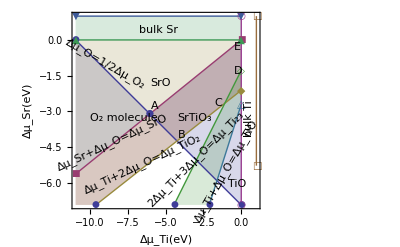

```mathematica
set2={{-10.95,0},{0,-6.93}};
set3={{-10.95,0},{0,-6.93}};
set4={{-10.95,-6.93},{0.,0}};
set5={{-10.95,-5.63},{0.,0}};
set6={{-10.95,-7.6},{0,-2.115}};
set7={{-10.95,0},{0,0}};
set8={{-10.95,1},{0,1}};
set9={{0,-6.93},{0,1}};
set10={{1,-5.28},{1,1}};
set11={{-10.95,-15.20},{0,-1.275}};
set12={{-4.63,-11.96},{0,-2.7}};


ListPlot[{set3,set5,set6,set7,set8,set9,set10,set11,set12},PlotRange->{{-10.95,1},{1,-6.93}},Joined->True,Frame->True,PlotStyle->Thick, Filling->True,LabelStyle->Directive[Medium,FontFamily->"Helvetica"],PlotMarkers->{Automatic},FrameLabel->{"Δμ_Ti(eV)","Δμ_Sr(eV)","",""},Axes->True,AxesLabel->{"Graphics[{Arrowheads[.1], Arrow[{{0.1, 0.0}, {.5, 0}}]}]","bal"}, FrameTicks->{{True,True},{True,True}},Axes->{True,True}, Epilog->{{Text["TiO",{-.9,-6.25},{-1,-1}]},{Text["Ti_2O_3",{20,-2.9},{-1,-1}]},{Text["SrTiO_3",{-4.2,-3.5},{-1,-1}]},{Text["O_2 molecule",{-10,-3.5},{-1,-1}]},{Text["SrO",{-6,-2.},{-1,-1}]},{Text["A",{-6,-3},{-1,-1}]},{Text["B",{-4.2,-4.2},{-1,-1}]},{Text["C",{-1.8,-2.85},{-1,-1}]},{Text["D",{-.5,-1.5},{-1,-1}]},{Text["E",{-.5,-.5},{-1,-1}]},Inset[Rotate[Text["Δμ_O=1/2Δμ_O_2"],-30 Degree],{-9,-1}],Inset[Rotate[Text["Δμ_Sr+Δμ_O=Δμ_SrO"],25 Degree],{-8.5,-4.3}],Inset[Rotate[Text["Δμ_Ti+2Δμ_O=Δμ_TiO_2"],25Degree],{-6.5,-5.2}],Inset[Rotate[Text["2Δμ_Ti+3Δμ_O=Δμ_Ti_2_3"],45Degree],{-3.,-5.}],
Inset[Rotate[Text["Δμ_Ti+Δμ_O=Δμ_TiO"],60Degree],{-1,-5.5}],Inset[Rotate[Text["bulk Ti"],90Degree],{.5,-3.3}],Inset[Rotate[Text["bulk Sr"],0Degree],{-5.5,.4}]}
]
```

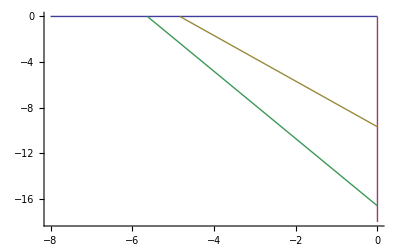

```mathematica
set2={{-8,0},{0,0}};
set3={{0,-18},{0,0}};
set9={{0,-9.67},{-4.835,0}};
set10={{0,-16.60},{-5.63,0}};
set11={{0,.5},{0,-5.53}};
set11={{0,.5},{0,-5.53}};
set12={{.5,.5},{.5,-5.53}};
ListPlot[{set2,set3,set9,set10},Joined->True,PlotStyle->Thick]
```

-16.5961

-9.6576

-5.6293

-2.1337

-9.55524

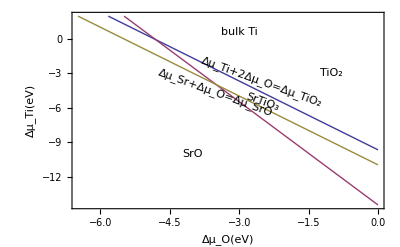

```mathematica
STO=-16.5961
Tio2=-9.6576
Sro=-5.6293
sr=-2.1337
ti=-9.55524475
set2={{-8,0},{0,0}};
set3={{0,-18},{0,0}};

aa=Plot[{{Tio2-2*o2},{STO-sr-3*o2},{STO-Sro-2*o2}},{o2,0,-17},PlotRange->{{1,-6},{2,-17}},Frame->{True,True,False,False},PlotStyle->Thick,FrameLabel->{"Δμ_O(eV)","Δμ_Ti(eV)","",""},Epilog->{Inset[Rotate[Text["bulk Ti"],0Degree],{-3,0.6}],Inset[Rotate[Text[""],90Degree],{.5,-8}],Inset[Rotate[Text["Δμ_Ti+2Δμ_O=Δμ_TiO_2"],-20Degree],{-2.5,-3.72}],Inset[Rotate[Text["Δμ_Sr+Δμ_O=Δμ_SrO"],-20 Degree],{-3.5,-4.70}],Inset[Rotate[Text["TiO_2"],0Degree],{-1,-3}],Inset[Rotate[Text["SrTiO_3"],-20Degree],{-2.5,-5.5}],Inset[Rotate[Text["SrO"],0Degree],{-4,-10}]}]
bb=Plot[{STO-Sro-2*o2},{o2,5,-30}];
cc=Plot[{STO-sr-3*o2},{o2,5,-30}];
```

```mathematica
data11=Import["/Users/masud/Desktop/STO/chk","Table"];
zz=data11[[All,{1,2}]];
zz1=data11[[All,{1,3}]];
zz2=data11[[All,{1,4}]];


lp=ListPlot[zz,Joined->True,Frame->{True,All,True,True},FrameLabel->{"","","","C_(o - o)/C_o"},FrameTicks->{{All,All},{None,None}}]
lp1=ListPlot[zz1,Joined->True,PlotRange->{{-5.5,-4},{.1,20}},Frame->{False,False,False,True},FrameStyle->{Automatic,Automatic,Automatic,Blue}];
lp2=ListPlot[zz2,Joined->True,PlotRange->{{-5.5,-4},{.1,20}},Frame->{False,False,False,True}];
```

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

ListPlot[Symbol[],Joined→True,Frame→{True,All,True,True},FrameLabel→{,,,C_(o - o)/C_o},FrameTicks→{{All,All},{None,None}}]

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

```mathematica
Overlay[{aa,lp}]
```

-Graphics-ListPlot[Symbol[],Joined→True,Frame→{True,All,True,True},FrameLabel→{,,,C_(o - o)/C_o},FrameTicks→{{All,All},{None,None}}]

```mathematica
Overlay[{aa,lp}];
```

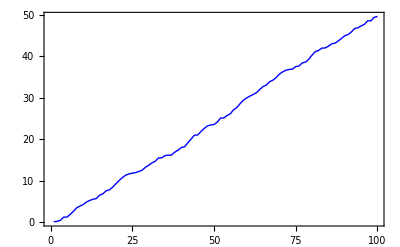

```mathematica
plot1=ListLinePlot[Accumulate[RandomReal[{0,1},{100}]],PlotStyle->Blue,ImagePadding->25,Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

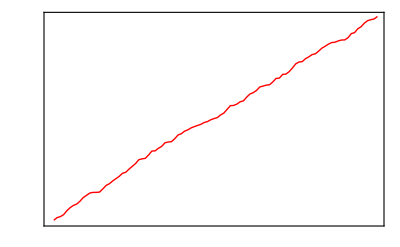

```mathematica
plot2=ListLinePlot[Accumulate[RandomReal[{0,100},{100}]],PlotStyle->Red,ImagePadding->25,Axes->False,Frame->{False,False,False,True},FrameTicks->{None,None,None,All},FrameStyle->{Automatic,Automatic,Automatic,Red}]
```

```mathematica
Overlay[{plot1,plot2}]
```

-Graphics--Graphics-